# 分布函数

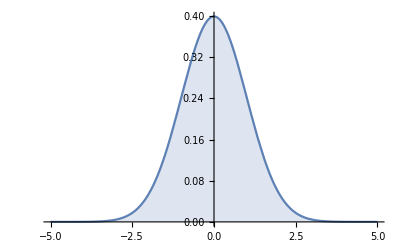

```mathematica
Plot[PDF[NormalDistribution[],x],{x,-5,5},Filling->Axis]
```

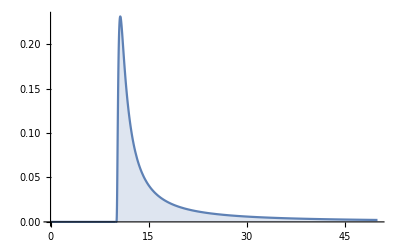

```mathematica
Plot[PDF[StableDistribution[1,0.5,1,10,2],x],{x,0,50},PlotRange->All,Filling->Axis]
```

```mathematica
Plot[PDF[LevyDistribution[10,2],x],{x,0,50},PlotRange->All,Filling->Axis]
```

-Graphics-

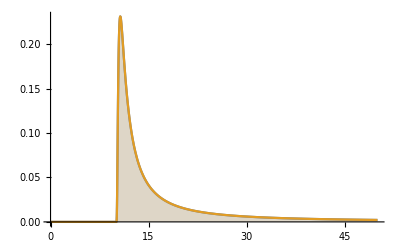

```mathematica
Plot[{PDF[StableDistribution[1,0.5,1,10,2],x],PDF[LevyDistribution[10,2],x]},{x,0,50},PlotRange->All,Filling->Axis]
```

### levy分布是稳态分布的特例，1,0.5,1

```mathematica
Manipulate[Plot[PDF[LevyDistribution[],x],{x,-10,10}],{}]
```